Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210407_sliding_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

Data with Sliding Time Windows

```mathematica
x=Round@Ceiling[Length@datafull/10,1];{a,b,c,d,e,f,g,h,i,j}=Join[Range[x,Length@datafull,x],{Length@datafull}];
data=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{k[[1]]-x/2,k[[2]]-x/2}],Take[datafull,{k[[1]],k[[2]]}]},{k,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win=Length@data
```

19

```mathematica
<<IGraphM`
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

Investigation of Constraints Impact in Time Windows

Girvan & Newman Modularity

M.E.J.Newman, Modularity and community structure in networks (2006).

```mathematica
,
```

```mathematica
,
```

```mathematica
GirvanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q,div1,div2,moditer,r1,r11,r12,r2,r21,r22,subfinal1Q,subfinal2Q,finalQ},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x≥0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β][[1]]]])^2,{i,VertexList@network}]*β))/(4*m);
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Positive];
moditer[pos_,B1_]:=Module[{Bg,ug,βg,sg,deltaQ,divv1,divv2,Bg1,Bg2},
Bg=(Table[B1[[i,j]]-KroneckerDelta[i,j]*Total@B1[[i,pos]],{i,Length@B1},{j,Length@B1}])[[pos,pos]];
ug=Eigenvectors@Bg;
βg=Eigenvalues@Bg;
sg=(ug/.x_/;x<0->-1)/.x_/;x≥0->1;
deltaQ=(Total@(Table[(ug[[i]].Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]])^2,{i,Range@Length@pos}]*βg))/(4*m);
divv1=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Negative];
divv2=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Positive];{deltaQ,divv1,divv2,Bg}];
r1=moditer[div1,B];
r11=If[r1[[1]]>0.001,moditer[r1[[2]],r1[[4]]],{0,0,0,0}];
r12=If[r1[[1]]>0.001,moditer[r1[[3]],r1[[4]]],{0,0,0,0}];
r2=moditer[div2,B];
r21=If[r2[[1]]>0.001,moditer[r2[[2]],r2[[4]]],{0,0,0,0}];
r22=If[r2[[1]]>0.001,moditer[r2[[3]],r2[[4]]],{0,0,0,0}];
subfinal1Q=If[r1[[1]]>0.001,If[r11[[1]]>0.001,If[r12[[1]]>0.001,r12[[1]]+r11[[1]]+r1[[1]],r11[[1]]+r1[[1]]],If[r12[[1]]>0.001,r12[[1]]+r1[[1]],r1[[1]]]],0];
subfinal2Q=If[r2[[1]]>0.001,If[r21[[1]]>0.001,If[r22[[1]]>0.001,r22[[1]]+r21[[1]]+r2[[1]],r21[[1]]+r2[[1]]],If[r22[[1]]>0.001,r22[[1]]+r2[[1]],r2[[1]]]],0];
finalQ=Q+subfinal1Q+subfinal2Q]
```

Assortativity Modularity (Wolfram)

where m is the number of edges,
A is the adjacency matrix,
 is the degree of node i,
 is the community that node i belongs to, 
 is the Kronecker δ symbol. 

For weighted graphs, 
A is the weighted adjacency matrix, 
 are the sum of weights of edges incident on node i,
m is the sum of all weights.

```mathematica
GraphAssortativity[graph,communities,"Normalized"->False]
```

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,11,win];]
```

{106.17,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,3,2,2,2,3,2,3,3,3,3,2,3,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

$Aborted

{652.273,{{35.3057,41.1775,25.1894},{33.7077,44.7019,19.4057},{40.737,47.2864,25.4914},{48.0033,55.7058,30.7582},{34.8997,41.8256,25.0804},{44.3327,50.9015,34.8645},{43.9687,49.6974,32.5661},{32.9194,39.3897,21.4795},{38.2478,45.5536,27.2461},{34.8641,42.1988,24.4283},{22.2936,28.3673,8.58778},{30.2122,37.8305,16.8789},{33.7675,40.2103,17.7559},{39.327,45.6105,23.9017},{40.2902,47.9589,26.3322},{53.1354,60.9216,38.9997},{52.4367,60.299,39.4231},{39.65,49.9319,29.0095},{56.778,59.7286,42.791}}}

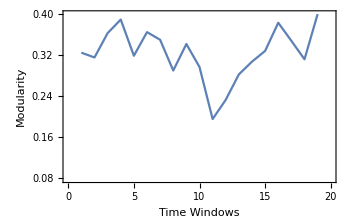
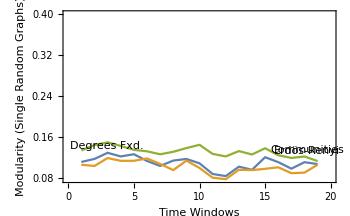
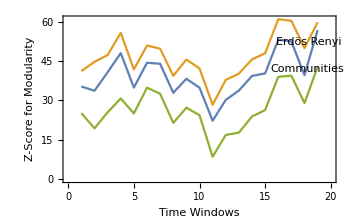

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,1,win];]
```

{28.7294,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,5,4,3,3,3,3,5,5,3,5,5,5,6,6,3,2,3,3}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{179.587,{{2.24328,4.6364,0.28054},{4.62374,6.81745,3.83219},{4.06222,5.10313,1.80302},{0.911019,1.23517,0.151496},{3.74984,5.27201,2.19419},{4.54895,5.89777,2.72343},{0.754816,1.40133,0.0589314},{1.98798,ComplexInfinity,1.14119},{0.0891397,ComplexInfinity,-0.14235},{3.29768,4.51544,2.58218},{4.24778,ComplexInfinity,2.35126},{1.05083,ComplexInfinity,-0.173203},{-0.266667,ComplexInfinity,-1.28414},{1.4015,ComplexInfinity,-0.449527},{-2.7074,ComplexInfinity,-2.18149},{3.95973,3.07364,4.20236},{-0.947356,0.395609,-1.0019},{-2.12805,-2.53497,-2.28751},{1.56469,1.89746,1.79123}}}

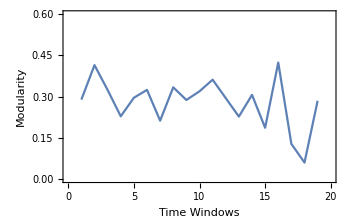
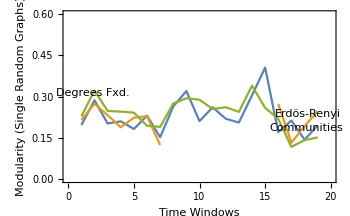
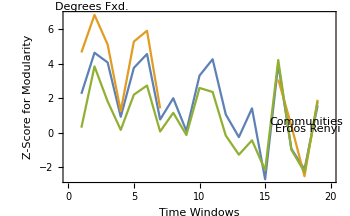

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},{0,0.6}}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},{0,0.6}},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,400,win];]
```

{131.112,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1116.13,{{36.3048,45.7662,17.9465},{38.5416,47.1353,20.2669},{39.7093,49.1397,22.7329},{37.8811,44.0101,20.4495},{41.9925,43.6797,19.8044},{48.1089,57.6757,30.1562},{49.743,59.4321,28.6981},{44.462,51.0102,24.3987},{42.1544,46.5508,23.7451},{38.0808,43.5325,22.5383},{22.7686,28.6384,6.22485},{17.7446,22.4644,1.7781},{23.7897,28.7794,4.96606},{23.3252,30.6115,8.73562},{27.8244,35.6486,14.6263},{39.2788,43.0586,21.3188},{31.4198,36.5992,13.1256},{25.0343,32.1539,10.8812},{35.8867,42.6362,19.2318}}}

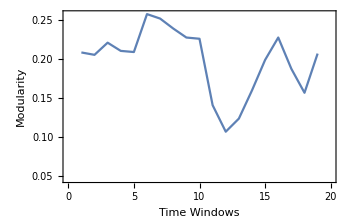
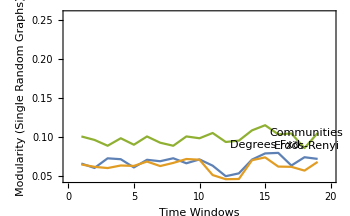
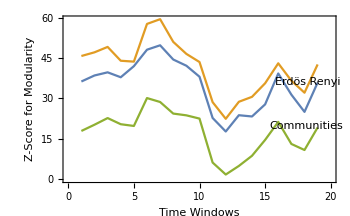

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,200,win];]
```

{175.759,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,2,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,2,3}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{1561.89,{{6.66327,14.1519,-4.70346},{3.59081,7.94066,-5.93657},{3.0193,8.04269,-8.53241},{1.58936,5.40099,-10.2015},{4.24288,7.78276,-8.60836},{5.63099,9.56213,-8.38675},{7.75241,13.5065,-5.78766},{-0.407631,4.49133,-10.9174},{6.58924,12.4533,-4.71857},{8.31737,11.086,-4.42077},{12.8278,17.973,-1.7048},{3.49658,6.82208,-7.23322},{8.1665,11.1287,-7.73329},{13.1754,18.8136,-1.50615},{4.81169,7.71161,-5.2671},{7.07698,11.2311,-4.04566},{3.03588,7.66659,-8.61946},{2.48344,6.00444,-6.81884},{8.30079,12.8397,-5.82129}}}

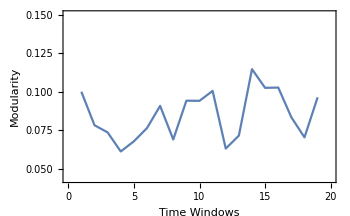
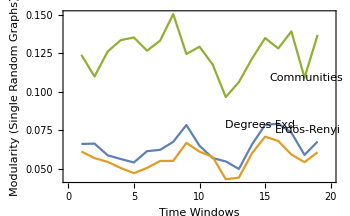
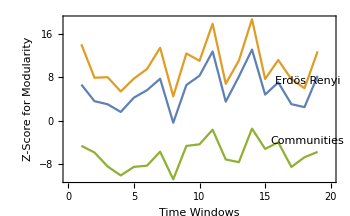

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,85,win];]
```

{11.6411,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,3,3,3,3,2,3,3,3,2,2,3,3,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{674.197,{{19.9517,24.5953,6.71262},{22.4703,30.3174,9.49572},{13.0865,17.8719,4.84692},{24.5639,26.2152,8.70302},{34.0139,38.6671,22.9823},{30.291,33.8416,17.5585},{28.982,32.5858,16.311},{26.5118,32.2956,14.2139},{23.5953,28.981,12.8076},{22.7166,27.0882,9.9077},{11.0775,14.4428,1.65294},{20.3159,26.4301,8.61585},{18.932,21.4588,4.11929},{15.706,20.546,3.46072},{27.6659,32.7021,17.9296},{26.1938,30.7882,13.6632},{13.0977,17.8141,3.22181},{28.8496,32.5315,13.5359},{42.4853,47.2469,29.5809}}}

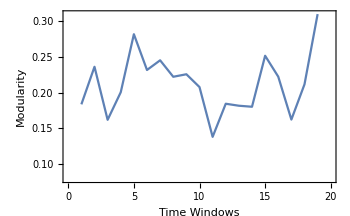
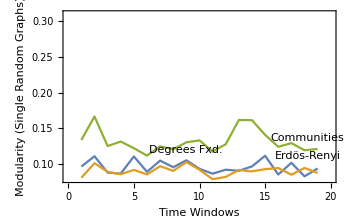
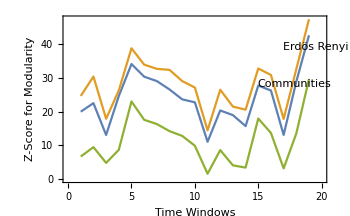

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,20,win];]
```

{11.0991,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,3,3,3,3,3,4,3,3,4,4,3,4,4,4,4}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{153.309,{{4.626,5.97768,3.24824},{2.54494,3.93234,2.52373},{3.48799,4.35918,2.09276},{0.895928,2.19475,-0.78432},{2.78646,3.53713,1.14509},{-0.0826569,0.89564,-0.692753},{5.23208,4.86439,5.48405},{1.1216,1.22374,1.19272},{2.76572,4.04495,1.76739},{1.30668,2.10012,1.21872},{1.73597,2.76158,1.35543},{2.07554,2.89086,1.97039},{-0.394555,0.0414356,-0.374884},{-0.748461,0.267806,-1.98424},{1.8442,2.77663,2.39552},{1.5491,1.29864,2.18096},{4.11408,4.27572,4.41499},{3.83876,4.00898,3.89917},{4.6785,4.54386,5.24469}}}

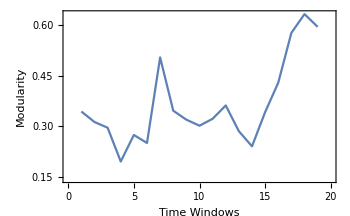
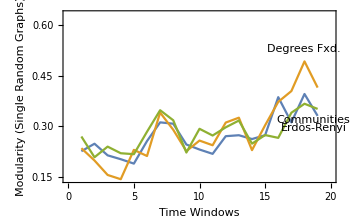
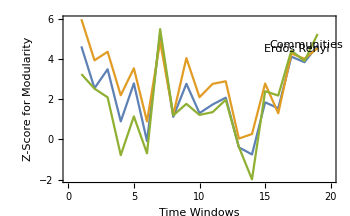

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,102,win];]
```

{13.2189,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{2087.57,{{20.1079,21.3411,-0.608433},{39.0788,41.434,12.528},{49.6163,54.956,20.6521},{57.2687,60.0657,29.9178},{53.8768,63.6948,28.2247},{57.0794,61.643,31.6596},{57.4551,60.3178,30.665},{60.9412,63.9665,32.9115},{51.1142,56.0938,25.2213},{34.5236,36.2002,13.9219},{28.3111,30.1371,7.18703},{31.5018,33.0946,5.87597},{32.9266,36.0686,7.24225},{24.4827,28.2734,7.42136},{38.0758,41.4232,19.4697},{43.1317,46.256,22.1368},{32.0511,34.462,11.3209},{38.2513,43.8234,16.7646},{48.0031,53.2938,25.0789}}}

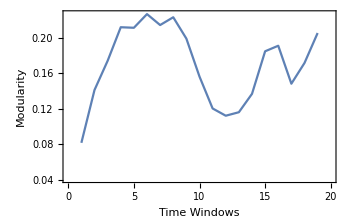
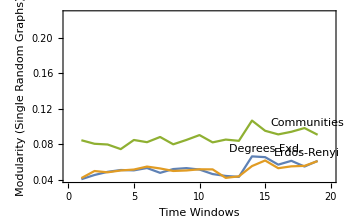
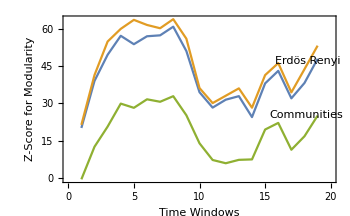

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,100,win];]
```

{13.6293,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@win}];
```

```mathematica
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,3,2,2,2,2,2,3,2,2,3,2,2}

```mathematica
singlerandomgraphserdren=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomerdrenmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphserdren[[i]],FindGraphCommunities[singlerandomgraphserdren[[i]]],"Normalized"->False],{i,Length@singlerandomgraphserdren}];
singlerandomgraphsdegreesfxd=Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@i],
Method->"VigerLatapy"],{i,graphsandnodenumbers[[All,1]]}];
singlerandomdegreesfxdmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphsdegreesfxd[[i]],FindGraphCommunities[singlerandomgraphsdegreesfxd[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegreesfxd}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
```

```mathematica
AbsoluteTiming[ZscoresmodularityWolf=Table[randomnessfunctionformodularity[i,"Wolf"],{i,graphsandnodenumbers[[All,1]]}]]
```

{2513.2,{{29.8044,32.519,9.75827},{28.1802,31.5399,8.15954},{19.7441,25.7591,3.99431},{30.2733,34.6911,10.1937},{24.4371,27.2402,4.76289},{27.3578,28.7374,8.14229},{13.1644,15.235,-1.21205},{27.6428,34.1745,7.67777},{22.676,24.5666,2.88235},{21.0122,22.9561,5.14344},{24.9155,25.357,5.39289},{23.1528,25.8017,3.73385},{11.351,12.5308,-3.697},{13.7384,15.4951,-1.1473},{23.8281,29.773,14.2404},{27.0149,28.4378,8.95967},{17.3095,19.5814,-2.14829},{16.3392,19.0258,1.97887},{22.237,25.3106,4.40487}}}

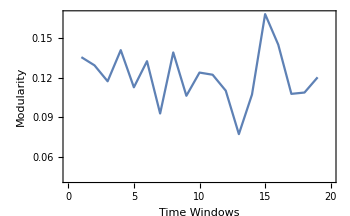
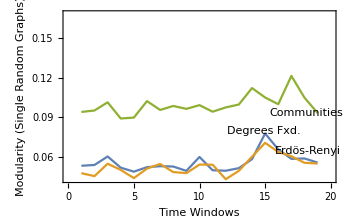
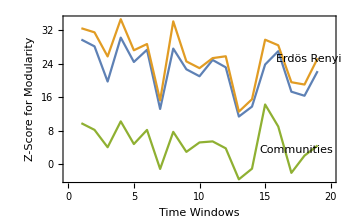

```mathematica
{ListLinePlot[Thread[{Range@win,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]}],ListLinePlot[{Thread[{Range@win,singlerandomerdrenmodularityvalues}],Thread[{Range@win,singlerandomdegreesfxdmodularityvalues}],Thread[{Range@win,singlerandomcommmodularityvalues}]},Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{0,win+1},MinMax[{modularityvalues,singlerandomerdrenmodularityvalues,singlerandomdegreesfxdmodularityvalues,singlerandomcommmodularityvalues}]},PlotLabels->Placed[{"Erdös-Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]],ListLinePlot[{Thread[{Range@win,ZscoresmodularityWolf[[All,1]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,2]]}],Thread[{Range@win,ZscoresmodularityWolf[[All,3]]}]},Frame->True,FrameLabel->{"Time Windows","Z-Score for Modularity"},ImageSize->350,PlotRange->{{0,win+1},All},PlotLabels->Placed[{"Erdös Renyi","Degrees Fxd.","Communities"},{Scaled[1],Above}]]}
```

Plots for Network Metrics and Z-scores

Modeling Works with OR Methods

FBA Model Reproducing from Kauffman et al. 2003

```mathematica
stochmatrix={{-1,-1,1,0,1,0,0},{1,0,0,1,0,-1,0},{0,1,-1,-1,0,0,-1}};
objectivefunc1={2,0,0,1,0,0,0};
objectivefunc2={1,0,0,2,0,0,0};
boundaries={{0,Infinity},{0,Infinity},{0,0},{0,Infinity},{0,1},{0,2},{0,0}};
steadystatevector={{0,0},{0,0},{0,0}};
Vvector={v1,v2,v3,v4,b1,b2,b3};
```

stochmatrix . Vvector = steadystatevector  ,   -objectivefunc ∈ solution space within boundaries
A, B, and C are metabolites. , , , and  are reactions. , , and  are flux exchanges.

```mathematica
Print["1st objective function solution vector: ",Vvector1=LinearProgramming[-objectivefunc1,stochmatrix,steadystatevector,boundaries]]
Print["2nd objective function solution vector: ",Vvector2=LinearProgramming[-objectivefunc2,stochmatrix,steadystatevector,boundaries]]
```

1st objective function solution vector: {1,0,0,0,1,1,0}

2nd objective function solution vector: {0,1,0,1,1,1,0}

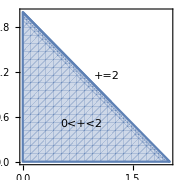

```mathematica
Show[RegionPlot[0<+<2,{,0,2},{,0,2},Frame->True,PlotLabels->Placed["0<+<2",{0.8,0.5}],FrameLabel->{"",""}],Plot[-+2,{,0,1.2},Frame->True,PlotLabels->Placed["+=2",{1.1,1}]],PlotRange->All,ImageSize->Small]
```

```mathematica
FindMaximum[{v4+2v1,-v1-v2+v3+b1==0&&v1+v4-b2==0&&v2-v3-v4-b3==0&&0≤v1+v2≤1&&0≤v1+v4≤2&&v2-v4==0&&0≤b1≤1&&0≤b2≤2&&b3==0&&v1≥0&&v2≥0&&v3==0&&v4≥0},{v1,v2,v3,v4,b1,b2,b3}]
```

{2.,{v1→1.,v2→0.,v3→0.,v4→0.,b1→1.,b2→1.,b3→0.}}

```mathematica
AdjmatR=Transpose[stochmatrix].stochmatrix;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
AdjmatM=stochmatrix.Transpose[stochmatrix];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
```

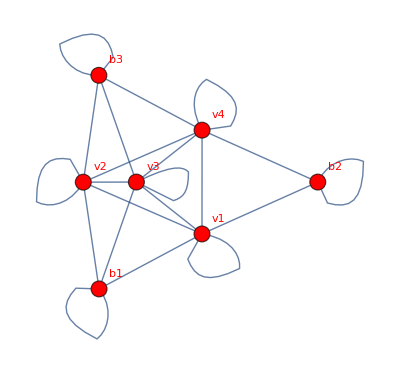
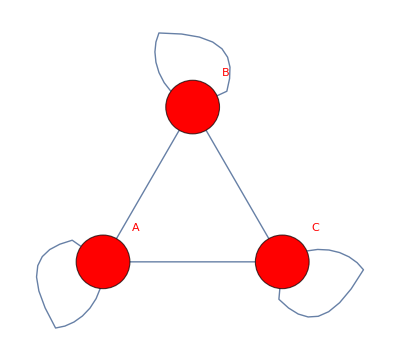

```mathematica
{AdjacencyGraph[NormAdjmatR,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"v1",2->"v2",3->"v3",4->"v4",5->"b1",6->"b2",7->"b3"}}],AdjacencyGraph[NormAdjmatM,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"A",2->"B",3->"C"}}]}
```

Implementation Trials

```mathematica
stoichioforhomosapiens=Drop[Import["iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
SparseArray[…]
```

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=1008;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

```mathematica
Dimensions@Solutionvectors
```

{200,1008}

```mathematica
nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
```

```mathematica
strial=stoichioforhomosapiens[[All,Flatten@nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens]];
Dimensions@strial
```

{738,396}

```mathematica
stoichiometricmatrix=strial;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=396;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

```mathematica
nonzerocolumnsinsolutionvectorswithstrial=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
```

```mathematica
Dimensions@nonzerocolumnsinsolutionvectorswithstrial
```

{116,1}

```mathematica
strial2=strial[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial]];
Dimensions@strial2
```

{738,116}

```mathematica
stoichiometricmatrix=strial2;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=116;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

```mathematica
(* with 3rd trial, solution vectors resulted as zeros *)
```

```mathematica
nonzerocolumnsinsolutionvectorswithstrial2=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
nonzerocolumnsinsolutionvectorswithstrial2
```

{{22},{23},{25},{26},{39},{40},{51},{53},{54},{55},{56},{62},{63},{67},{73},{79},{81},{84},{85},{86},{87},{90},{91},{105},{108},{109}}

```mathematica
networkfeaturesdata=Solutionvectors[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial2]]*10^12;
```

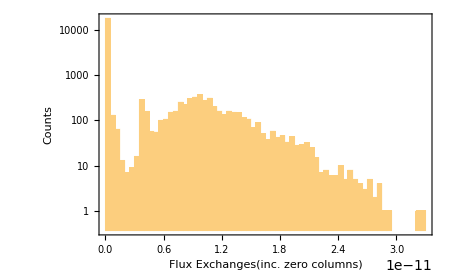
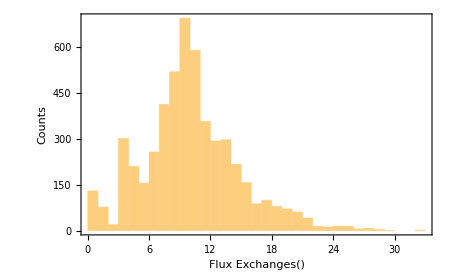

```mathematica
{Histogram[Flatten@Solutionvectors,Frame->True,ScalingFunctions->"Log",PlotRange->All,FrameLabel->{"Flux Exchanges(inc. zero columns)","Counts"},ImageSize->450],Histogram[Flatten@networkfeaturesdata,Frame->True,PlotRange->All,FrameLabel->{"Flux Exchanges()","Counts"},ImageSize->450]}
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=networkfeaturesdata;
Dimensions@data
```

{200,26}

```mathematica
snetworkgraphsinglenodes[data[[]]]
```

```mathematica
(* snetworkgraphsinglenodes[aim_,campaign_,vertexsize_,vertexlabelsize_,imagesize_,vertexcolor_] *)
```